## Load Data

```mathematica
SetDirectory[NotebookDirectory[]]
rawTuples=Import["parameter_sweep/tuple_names.csv","Table"]
rawEIR=Import["parameter_sweep/EIR_sweep.csv","Table"];
```

/Users/chipdelmal/Documents/School/Research/VCOM/OtherRoutines

{{epsilon0,species,OVIcov,time_OVI_on,FOGcov,time_FOG_on,LARcov,time_LAR_on,BIOcov,time_BIO_on,SREcov,time_SRE_on,IRScov,time_IRS_on,ITNcov,time_ITN_on,ECScov,time_ECS_on,ECTcov,time_ECT_on,HOUcov,time_HOU_on,OBTcov,time_OBT_on,SPRcov,time_SPR_on,PPMcov,time_PPM_on,ATSBcov,time_ATSB_on,SSPcov,time_SSP_on},{100,1,0,20,0,20,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{100,1,0.2,20,0,20,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{100,1,0.4,20,0,20,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{100,1,0.6,20,0,20,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{100,1,0.8,20,0,20,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{100,1,1,20,0,20,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{100,1,0,20,0.2,20,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{100,1,0.2,20,0.2,20,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},3218,{100,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0.8,20,0.8,20},{100,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,20,0.8,20},{100,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,20,1,20},{100,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0.2,20,1,20},{100,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0.4,20,1,20},{100,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0.6,20,1,20},{100,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0.8,20,1,20},{100,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,20,1,20}}
 |  |  |  |

## Run Analysis

```mathematica
{head,tuples,eir}={StringSplit[rawTuples[[1]],","][[1]],((ToExpression/@(StringSplit[#,","]))&/@rawTuples[[2;;All]])[[All,1]],(ToExpression/@rawEIR)[[All,1]]};
head2=Append[head,"EIR"];
data=Transpose[{tuples,eir}];
coverages=Range[0,1,.2];
controlVct=Flatten[{Range[3,tuples[[1]]//Length,2]}];
inOuts={#[[controlVct]]&/@tuples,eir}//Transpose;
```

## Plot

```mathematica
Grid[{{
ArrayPlot[inOuts[[All,1]],ImageSize->1000,Frame->None,AspectRatio->5,ColorFunction->"TemperatureMap",PlotLegends->Placed[Automatic,Left],PlotRangePadding->0],
ArrayPlot[Transpose[{inOuts[[All,2]]}],ImageSize->1000,Frame->None,AspectRatio->5,ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRangePadding->0]
}}];
(*Export["CoolAtari.png",%,ImageSize->2000,ImageResolution->100]*)
```

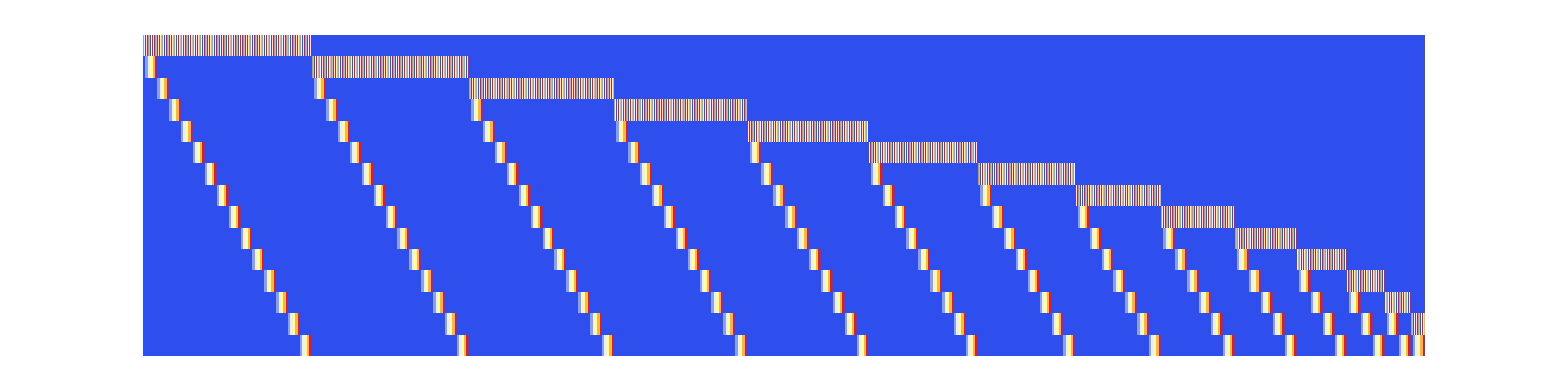
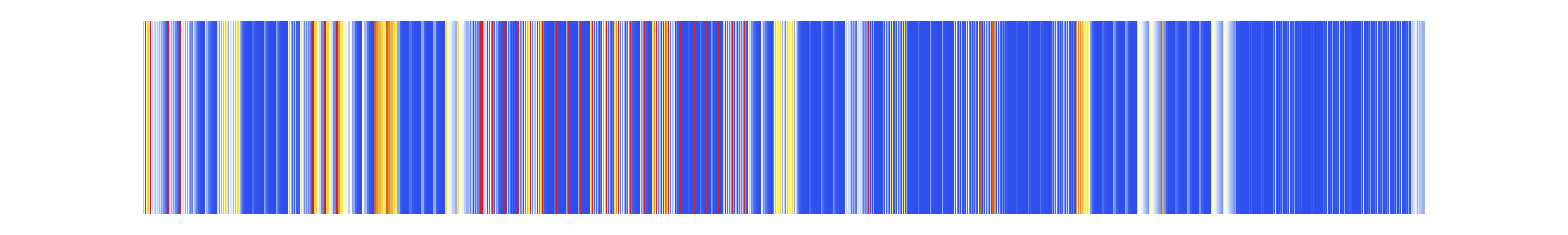

```mathematica
color="TemperatureMap";
img=Grid[{
{ArrayPlot[Transpose[inOuts[[All,1]]],ImageSize->2000,Frame->None,AspectRatio->.25,ColorFunction->color,PlotLegends->Placed[Automatic,Top],PlotRangePadding->0]},
{ArrayPlot[{inOuts[[All,2]]},ImageSize->2000,Frame->None,AspectRatio->.15,ColorFunction->color,PlotLegends->Placed[Automatic,Bottom],PlotRangePadding->0]}
}]
(*Export["CoolAtari2.png",%,ImageSize->2000,ImageResolution->300]*)
```

## Filter

```mathematica
{covTotal,eirValue}={.4,10};
filtered=Cases[inOuts,{a_,b_}/;Total[a]≤covTotal&&b≤eirValue];
Grid[Flatten[{{Append[head[[controlVct]],"EIR"]},Flatten/@filtered},1],Background->{None,{LightBlue}}]
(*Export["table.png",%]*)
```

OVIcov | FOGcov | LARcov | BIOcov | SREcov | IRScov | ITNcov | ECScov | ECTcov | HOUcov | OBTcov | SPRcov | PPMcov | ATSBcov | SSPcov | EIR
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 9.29741
0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 7.70485
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 2.13275
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 9.29741
0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 9.29741
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 2.13275
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 9.29741
0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 7.0135
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 2.13275
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 9.29741
0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 7.0135
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 2.13275
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 9.29741
0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 7.99577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 2.13275
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 9.29741
0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 4.63891
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 2.13275
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 9.29741
0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 4.95853
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 2.13275
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 9.29741
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 8.84346
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 2.13275
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 9.29741
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0.2 | 0 | 0 | 0 | 0 | 8.84346
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 2.13275
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 9.29741
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0.2 | 0 | 0 | 0 | 0 | 2.73838
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 2.13275
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0.2 | 0 | 0 | 0 | 5.95582
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0.2 | 0 | 0 | 5.95582
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 9.29741
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 0 | 2.13275
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0.2 | 0 | 0 | 0 | 2.73838
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0.2 | 0 | 0 | 2.73838
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0.2 | 0 | 7.29614
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0.2 | 7.29614
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0.2 | 0 | 0 | 5.95582
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 4.22577
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4 | 0 | 0 | 4.22577